Simulation of flexible beams or an n-link manipulator

```mathematica
SetDirectory[NotebookDirectory[]];
<<"rotationtools.wl"
```

Meta - parameters : 
Number of links - n and hence n rigid coordinates
Number of discretisations per link - Nl these are the flexible coordinates.

```mathematica
lin = 1;
disc=1;
```

Sim required from meta-data parameters. Assuming absolute angles throughout the sim. We can give density and area functions too. But assuming them to be constant here.
Source: Ghosal example problem

```mathematica
L = 1;
dat=SetPrecision[{Ep*Iy->1165.4916,Ep*Iz->1165.4916,g->9.81,ρ*A->0.331,lp->L/disc},15];
```

Forward Kinematics:
Transformation matrix for rigid part
Return a homogenous matrix

```mathematica
hom[rot_,trans_]:=Module[{},Return[Join[Join[rot,Transpose[{trans}],2],{{0,0,0,1}}]]];
```

Return the matrix multiplication from an input DH table
Or manual multiplication

```mathematica
T1=hom[rotZ[θ],{0,0,0}]
```

{{{Cos[θ1[t]]},{-Sin[θ1[t]]},0,0},{{Sin[θ1[t]]},{Cos[θ1[t]]},0,0},{0,0,1,0},{0,0,0,1}}

Assume straight single link for now

Shape functions

```mathematica
ψ = Together[Expand[{1-3(s/lp)^2+2(s/lp)^3,s(s/lp-1)^2,(s/lp)^2(3-2 s/lp),s^2/lp(s/lp-1)}]];
```

Now the partial of the position vectors. If there are Nl pieces we’ll have 4(Nl+1) flexible degrees of freedom since there is no twist and elongation considered.

```mathematica
Tf=hom[rotZ[ϕz],{0,0,0}].hom[rotZ[0],{0,0,δz}].hom[rotY[ϕy],{0,0,0}].hom[rotY[0],{0,δy,0}];
```

This is used at each discretisation to find the position vector of the corresponding discrete unit. Also generate the list of generalised coordinates. Ideally only the coordinates which are not zero are to be produced

```mathematica
θ=Table[Symbol["θ"<>ToString[i]][t],{i,lin}];
δy=Table[Table[Symbol["δy"<>ToString[i]<>ToString[j]][t],{j,disc+1}],{i,lin}];
δz=Table[Table[Symbol["δz"<>ToString[i]<>ToString[j]][t],{j,disc+1}],{i,lin}];
ϕy=Table[Table[Symbol["ϕy"<>ToString[i]<>ToString[j]][t],{j,disc+1}],{i,lin}];
ϕz=Table[Table[Symbol["ϕz"<>ToString[i]<>ToString[j]][t],{j,disc+1}],{i,lin}];
```

Deflection of any point at a distance `s` on the ith disc length is

Here it is assumed that all the links are planar and hence the FK is the product of length vector and the rotation matrix. In other cases one might want to use the DH parameters.

It seems to be practically impossible to integrate the Jacobian as is. So strategies for simplification are:
1. Reduce the complexity i.e. make it 2D
2. Assume it to be 3D but let the deflections be small
3. Device a strategy to do this numerically
4. Compute the lower triangular half of the M matrix
5. Interestingly using Together[] makes the computation faster
6. Apriori substitution of numbers

Starting with the second assumption. Elastic potential energy

```mathematica
d2ψ=D[ψ,{s,2}];
```

Formulating the mass matrix

```mathematica
qvec = Flatten[Join[θ,δy,δz,ϕy,ϕz]];
```

```mathematica
tic[]
M  = Table[Table[0,{jj,Length[qvec]}],{dd,Length[qvec]}];
(*PEg = Table[0,{jj,Length[qvec]}];
PEfy = Table[0,{jj,Length[qvec]}];
PEfz = Table[0,{jj,Length[qvec]}];*)
PEg =0;
PEfy =0;
PEfz =0;
pinit = {0,0,0};
For[j=1, j≤lin, j++,
For[i=2, i≤ disc+1, i++,
(*coordinates of any point at a distance "s" in a local frame of the ith link*)
pinit =(pinit/.s->lp)+rotZ[θ[[j]]].smallrotZ[ϕz[[j,i-1]]].smallrotY[ϕy[[j,i-1]]].{s,ψ.{δy[[j,i-1]],ϕy[[j,i-1]],δy[[j,i]],ϕy[[j,i]]},ψ.{δz[[j,i-1]],ϕz[[j,i-1]],δz[[j,i]],ϕz[[j,i]]}};
(*Print[{j,i}];*)
(*Print[pinit];*)
(*Computing the g matrix*)
gmat =Together[Transpose[D[pinit,{qvec}]].D[pinit,{qvec}]];
(*gmat =Transpose[D[pinit,{Flatten[Join[θ,δy,δz,ϕy,ϕz]]}]].D[pinit,{Flatten[Join[θ,δy,δz,ϕy,ϕz]]}];*)
(*D[pinit,{Join[θ,δy,δz,ϕy,ϕz]}]*)
(*Computing the mass matrix*)
M= M+ρ*A*Integrate[gmat,{s,0,lp}];
(*Computing the G matrix*)
PEg= PEg+ρ*A*Integrate[{g,0,0}.pinit,{s,0,lp}];
PEfy= PEfy+Ep*Iy/2*Integrate[Together[(d2ψ.{δy[[j,i-1]],ϕy[[j,i-1]],δy[[j,i]],ϕy[[j,i]]})^2],{s,0,lp}];
PEfz= PEfz+Ep*Iz/2*Integrate[Together[(d2ψ.{δz[[j,i-1]],ϕz[[j,i-1]],δz[[j,i]],ϕz[[j,i]]})^2],{s,0,lp}];
]
]
toc[]
```

Actual time consumed: 22.242866 seconds.

CPU time consumed: 21.923 seconds.

Checking the symmetric nature

```mathematica
M-Transpose[M]
```

{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}

```mathematica
Mmat = M//Simplify;
qt = qvec;
```

```mathematica
Mmat//Variables
```

{A,lp,ρ,δy11[t],δy12[t],δz11[t],δz12[t],ϕy11[t],ϕy12[t],ϕz11[t],ϕz12[t]}

Assuming that everything is working moving on to C mat

```mathematica
tic[]
nn = Length[qvec];
tempC = Table[0, {ii, 1,nn}, {jj, 1,nn}];
For [ii= 1, ii≤ nn, 
For[jj = 1, jj ≤ nn,
For[kk = 1, kk≤ nn, 
tempC[[ii,jj]] +=1/2*( D[Mmat[[ii,jj]], qt[[kk]]] + D[Mmat[[ii,kk]], qt[[jj]]] - D[Mmat[[jj, kk]], qt[[ii]]])*D[qt[[kk]],t] ;
kk++];
jj++];
ii++];
toc[]
```

Actual time consumed: 0.053397 seconds.

CPU time consumed: 0.047 seconds.

```mathematica
tempC//Variables
```

{A,lp,ρ,δy11[t],δy12[t],δz11[t],δz12[t],ϕy11[t],ϕy12[t],ϕz11[t],ϕz12[t],δy11'[t],δy12'[t],δz11'[t],δz12'[t],θ1'[t],ϕy11'[t],ϕy12'[t],ϕz11'[t],ϕz12'[t]}

```mathematica
Mmat/.dat/.dat//Simplify//Variables
```

{δy11[t],δy12[t],δz11[t],δz12[t],ϕy11[t],ϕy12[t],ϕz11[t],ϕz12[t]}

```mathematica
Cmat = tempC;
```

Validating the Cmat

```mathematica
tic[]
Amat = D[Mmat,t] - 2*Cmat;
toc[]
```

Actual time consumed: 0. seconds.

CPU time consumed: 0. seconds.

```mathematica
(Amat+ Transpose[Amat])//FullSimplify
```

{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}

Computing the Gmat

```mathematica
PE = PEfy+PEfz+PEg;
G  = D[PE,{qvec}]//Simplify;
G//Dimensions
```

{9}

```mathematica
G/.cond
```

{1/12 A g lp ρ (-6 lp Sin[θ1[t]]-Cos[θ1[t]] (6 δy12[t]-lp ϕy12[t])),-1/2 A g lp ρ Sin[θ1[t]]+(6 Ep Iy (-2 δy12[t]+lp ϕy12[t]))/lp^3,-(A g lp^4 ρ Sin[θ1[t]]-24 Ep Iy δy12[t]+12 Ep Iy lp ϕy12[t])/(2 lp^3),(6 Ep Iz (-2 δz12[t]+lp ϕz12[t]))/lp^3,-(6 Ep Iz (-2 δz12[t]+lp ϕz12[t]))/lp^3,(2 Ep Iy (-3 δy12[t]+lp ϕy12[t]))/lp^2-1/12 A g lp ρ (lp Sin[θ1[t]]-Cos[θ1[t]] (6 δz12[t]-lp ϕz12[t])),(A g lp^4 ρ Sin[θ1[t]]-72 Ep Iy δy12[t]+48 Ep Iy lp ϕy12[t])/(12 lp^2),-1/12 A g lp ρ (6 lp Sin[θ1[t]]+6 Cos[θ1[t]] δy12[t]-lp Cos[θ1[t]] ϕy12[t])+(2 Ep Iz (-3 δz12[t]+lp ϕz12[t]))/lp^2,(2 Ep Iz (-3 δz12[t]+2 lp ϕz12[t]))/lp^2}

```mathematica
i=2;
j=1;
```

This completes the derivation of the equation of motion

```mathematica
(*cond=(*Inner[Rule,qvec,Table[0,{ll,Length[qvec]}],List]*){δy11[t]->0,δy12[t]->0,δy13[t]->0,δz11[t]->0,δz12[t]->0,δz13[t]->0,ϕy11[t]->0,ϕy12[t]->0,ϕy13[t]->0,ϕz11[t]->0,ϕz12[t]->0,ϕz13[t]->0}*)
```

{δy11[t]→0,δy12[t]→0,δy13[t]→0,δz11[t]→0,δz12[t]→0,δz13[t]→0,ϕy11[t]→0,ϕy12[t]→0,ϕy13[t]→0,ϕz11[t]→0,ϕz12[t]→0,ϕz13[t]→0}

```mathematica
(*cond=Inner[Rule,{δy11[t],δz11[t],ϕy11[t],ϕz11[t]},{0,0,0,0},List]*)
```

{δy11[t]→0,δz11[t]→0,ϕy11[t]→0,ϕz11[t]→0}

As given in Ghosal which cites Book 1985 that the clamped end should have no generalised force corresponding it. Also the clamped boundary condition is represented by setting the δy11 δz11 ϕy11 ϕy11 to zero. Obtaining the lower order model after enforcing these constraints.

```mathematica
Mnew=Transpose[{Mmat[[;;,1]],Mmat[[;;,3]],Mmat[[;;,5]],Mmat[[;;,7]],Mmat[[;;,9]]}];
```

```mathematica
Mnew2={Mnew[[1,;;]],Mnew[[3,;;]],Mnew[[5,;;]],Mnew[[7,;;]],Mnew[[9,;;]]};
```

```mathematica
qnew= qvec[[{1,3,5,7,9}]];
```

```mathematica
cond=Join[Inner[Rule,{δy11[t],δz11[t],ϕy11[t],ϕz11[t]},{0,0,0,0},List],D[Inner[Rule,{δy11[t],δz11[t],ϕy11[t],ϕz11[t]},{0,0,0,0},List],t]]
```

{δy11[t]→0,δz11[t]→0,ϕy11[t]→0,ϕz11[t]→0,δy11'[t]→0,δz11'[t]→0,ϕy11'[t]→0,ϕz11'[t]→0}

```mathematica
Mmat2 =SetPrecision[Mnew2/.dat/.dat,15]/.cond;
```

```mathematica
Mmat2//Variables
```

{δy12[t],ϕy12[t]}

```mathematica
(*Mmat3= Drop[Mmat2,0,{2,13,3}]//Dimensions*)
```

{13,9}

Compile all the matrices

```mathematica
(*cMmat = Compile[{{θ1[t],_Real},{δy11[t],_Real},{δy12[t],_Real},{δy13[t],_Real},{δz11[t],_Real},{δz12[t],_Real},{δz13[t],_Real},{ϕy11[t],_Real},{ϕy12[t],_Real},{ϕy13[t],_Real},{ϕz11[t],_Real},{ϕz12[t],_Real},{ϕz13[t],_Real}}, Evaluate[Mmat2]];*)
```

```mathematica
cMmat = Compile[{{θ1[t],_Real},{δy12[t],_Real},{δz12[t],_Real},{ϕy12[t],_Real},{ϕz12[t],_Real}}, Evaluate[Mmat2]];
```

```mathematica
cMmat@@RandomReal[{0,100},5];
```

In Ghosal the stiffness matrix is given separately again but this should be accounted in the strain PE computed

```mathematica
Cnew=Transpose[{Cmat[[;;,1]],Cmat[[;;,3]],Cmat[[;;,5]],Cmat[[;;,7]],Cmat[[;;,9]]}];
```

```mathematica
Cmat//Variables
```

{A,lp,ρ,δy11[t],δy12[t],δz11[t],δz12[t],ϕy11[t],ϕy12[t],ϕz11[t],ϕz12[t],δy11'[t],δy12'[t],δz11'[t],δz12'[t],θ1'[t],ϕy11'[t],ϕy12'[t],ϕz11'[t],ϕz12'[t]}

```mathematica
Cmat2 =SetPrecision[Cmat/.dat/.dat,15]/.cond;
```

```mathematica
Cmat2//Variables
```

{δy12[t],δz12[t],ϕy12[t],ϕz12[t],δy12'[t],δz12'[t],θ1'[t],ϕy12'[t],ϕz12'[t]}

```mathematica
(*cCmat = Compile[{{θ1[t],_Real},{δy11[t],_Real},{δy12[t],_Real},{δy13[t],_Real},{δz11[t],_Real},{δz12[t],_Real},{δz13[t],_Real},{ϕy11[t],_Real},{ϕy12[t],_Real},{ϕy13[t],_Real},{ϕz11[t],_Real},{ϕz12[t],_Real},{ϕz13[t],_Real},{θ1'[t],_Real},{δy11'[t],_Real},{δy12'[t],_Real},{δy13'[t],_Real},{δz11'[t],_Real},{δz12'[t],_Real},{δz13'[t],_Real},{ϕy11'[t],_Real},{ϕy12'[t],_Real},{ϕy13'[t],_Real},{ϕz11'[t],_Real},{ϕz12'[t],_Real},{ϕz13'[t],_Real}}, Evaluate[Cmat2]];*)
```

```mathematica
cCmat = Compile[{{θ1[t],_Real},{δy12[t],_Real},{δz12[t],_Real},{ϕy12[t],_Real},{ϕz12[t],_Real},{θ1'[t],_Real},{δy12'[t],_Real},{δz12'[t],_Real},{ϕy12'[t],_Real},{ϕz12'[t],_Real}}, Evaluate[Cmat2]];
```

```mathematica
cCmat@@RandomReal[{0,100},10];
```

```mathematica
Gmat=SetPrecision[ G/.dat/.dat,15]/.cond;
```

```mathematica
Gmat//Variables
```

{Cos[θ1[t]],Sin[θ1[t]],δy12[t],δz12[t],ϕy12[t],ϕz12[t]}

```mathematica
cGmat = Compile[{{θ1[t],_Real},{δy12[t],_Real},{δz12[t],_Real},{ϕy12[t],_Real},{ϕz12[t],_Real}}, Evaluate[Gmat]];
```

```mathematica
cGmat@@RandomReal[{0,100},5];
```

Write a module for simulating dynamics

```mathematica
(*Formulating the double dots*)
doubledots[q_?(VectorQ[#,NumericQ]&),dq_?(VectorQ[#,NumericQ]&)]:=Module[{Mval, Cval, Gval, LHS},
Mval=cMmat@@q;
Cval=cCmat@@Join[q,dq];
Gval=cGmat@@q;
LHS=-(Inverse[Mval]).(Cval.dq+Gval);
Return[LHS];
];
```

```mathematica
qvec//Dimensions
```

{9}

```mathematica
LinearSolve[cMmat@@Join[{-π/2},Table[0,{jj,4}]],cGmat@@Join[{-π/2},Table[0,{jj,4}]]]
```

LinearSolve::nosol: Linear equation encountered that has no solution.

LinearSolve[{{0.110333,0.11585,0.,-0.01655,0.},{0.04965,0.0425571,0.,-0.0102452,0.},{0.11585,0.122943,0.,-0.0173381,0.},{0.,0.,0.0425571,0.,-0.0102452},{0.,0.,0.122943,0.,-0.0173381},{0.0110333,0.0102452,-0.11585,-0.00236429,0.01655},{-0.01655,-0.0173381,0.,0.00315238,0.},{0.110333,0.11585,0.0102452,-0.01655,-0.00236429},{0.,0.,-0.0173381,0.,0.00315238}},{1.62356,1.62356,1.62356,0.,0.,0.270593,-0.270593,1.62356,0.}]

```mathematica
cMmat@@Join[{-π/2},Table[0,{jj,4}]]//Dimensions
```

{9,5}

```mathematica
cCmat@@Join[Join[{-π/2},Table[0,{jj,4}]],Table[0,{jj,5}]]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.}}

```mathematica
cGmat@@Join[{-π/2},Table[0,{jj,4}]]
```

{1.62356,1.62356,1.62356,0.,0.,0.270593,-0.270593,1.62356,0.}

```mathematica
SetPrecision[doubledots[Join[{-π/2},Table[0,{jj,4}]],Table[0,{jj,5}]],15]
```

Inverse::matsq: Argument {{0.110333,0.11585,0.,-0.01655,0.},{0.04965,0.0425571,0.,-0.0102452,0.},{0.11585,0.122943,0.,-0.0173381,0.},«3»,{-0.01655,-0.0173381,0.,0.00315238,0.},{0.110333,0.11585,0.0102452,-0.01655,-0.00236429},{0.,0.,-0.0173381,0.,0.00315238}} at position 1 is not a non-empty square matrix.

Dot::dotsh: Tensors {{0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.}} and {0,0,0,0,0} have incompatible shapes.

Inverse::matsq: Argument {{0.110333,0.11585,0.,-0.01655,0.},{0.04965,0.0425571,0.,-0.0102452,0.},{0.11585,0.122943,0.,-0.0173381,0.},«3»,{-0.01655,-0.0173381,0.,0.00315238,0.},{0.110333,0.11585,0.0102452,-0.01655,-0.00236429},{0.,0.,-0.0173381,0.,0.00315238}} at position 1 is not a non-empty square matrix.

Inverse::matsq: Argument {{0.110333333333333,0.11585,0,-0.01655,0},{0.04965,0.0425571428571429,0,-0.0102452380952381,0},«6»,{0,0,-0.0173380952380952,0,0.00315238095238095}} at position 1 is not a non-empty square matrix.

General::stop: Further output of Inverse::matsq will be suppressed during this calculation.

Dot::dotsh: Tensors {{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}} and {0,0,0,0,0} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

-1. Inverse[{{0.110333333333333,0.11585,0,-0.01655,0},{0.04965,0.0425571428571429,0,-0.0102452380952381,0},{0.11585,0.122942857142857,0,-0.0173380952380952,0},{0,0,0.0425571428571429,0,-0.0102452380952381},{0,0,0.122942857142857,0,-0.0173380952380952},{0.0110333333333333,0.0102452380952381,-0.11585,-0.00236428571428571,0.01655},{-0.01655,-0.0173380952380952,0,0.00315238095238095,0},{0.110333333333333,0.11585,0.0102452380952381,-0.01655,-0.00236428571428571},{0,0,-0.0173380952380952,0,0.00315238095238095}}].{1.623555+{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}.{0,0,0,0,0},1.623555+{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}.{0,0,0,0,0},1.623555+{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}.{0,0,0,0,0},{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}.{0,0,0,0,0},{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}.{0,0,0,0,0},0.2705925+{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}.{0,0,0,0,0},-0.2705925+{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}.{0,0,0,0,0},1.623555+{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}.{0,0,0,0,0},{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}.{0,0,0,0,0}}

```mathematica
doubledots[RandomReal[{0,10},13],RandomReal[{0,10},13]]
```

{-272460.,2.29593×10^6,1.54487×10^7,1.15104×10^7,3.35162×10^6,-3.87581×10^6,-1.39056×10^6,-1.28446×10^7,1.51236×10^7,2.07314×10^7,-3.07609×10^7,-9.70453×10^6,-7.53689×10^6}

```mathematica
tf = 1;
tic[]
dynsim = NDSolve[{SetPrecision[doubledots[q1[t],q1'[t]],15]==q1''[t],q1[0]==Join[{π/18},Table[0,{jj,Length[qvec]-1}]],q1'[0]==Table[0,{jj,Length[qvec]}]},q1,{t,0,tf}][[1]]
toc[]
```

{q1→InterpolatingFunction[{{0., 1.}}, <>]}

Actual time consumed: 14.216759 seconds.

CPU time consumed: 14.141 seconds.

```mathematica
qvals  =Table[(q1[jj]/.dynsim),{jj,0,tf,0.01}];
```

```mathematica
qvals//Length
```

101

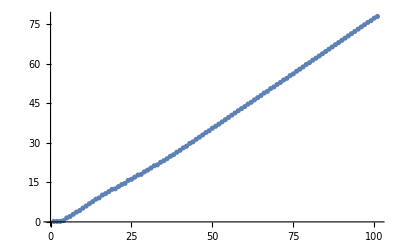

```mathematica
θvals  =Table[(q1[jj]/.dynsim)[[1]],{jj,0,tf,0.01}];
ListPlot[θvals]
```

For visualisation use 10 point discretisation between two nodes

```mathematica
plist={};
pinit = {0,0,0};
For[j=1, j≤lin, j++,
For[i=2, i≤ disc+1, i++,
pinit =(pinit/.s->lp)+rotZ[θ[[j]]].smallrotZ[ϕz[[j,i-1]]].smallrotY[ϕy[[j,i-1]]].{s,ψ.{δy[[j,i-1]],ϕy[[j,i-1]],δy[[j,i]],ϕy[[j,i]]},ψ.{δz[[j,i-1]],ϕz[[j,i-1]],δz[[j,i]],ϕz[[j,i]]}};
AppendTo[plist,pinit/.dat/.dat]
]
]
```

Positions of the nodes

```mathematica
p2s=Table[Symbol["p2s"<>ToString[j]],{j,Length[svals]}];
p1s=Table[Symbol["p1s"<>ToString[j]],{j,Length[svals]}];
```

```mathematica
For[dd=1, dd≤ Length[svals], dd++,
p2s[[dd]]={};
p1s[[dd]]={};
For[ll=1, ll≤ Length[qvals], ll++,
tempp2=plist[[2]]/.svals[[dd]]/.cond/.Inner[Rule,qvec,qvals[[ll]],List];
tempp1=plist[[1]]/.svals[[dd]]/.cond/.Inner[Rule,qvec,qvals[[ll]],List];
AppendTo[p2s[[dd]],tempp2];
AppendTo[p1s[[dd]],tempp1];
]
]
```

```mathematica
Manipulate[
Show[Graphics3D[{EdgeForm[Directive[Opacity[0]]],Opacity[0],Cuboid[{-1,-1,-0.1}, {1,1,0.1}]},Boxed->False,Axes->True,AxesLabel->{"X","Y","Z"}],Graphics3D[Sphere[{0,0,0},0.03]],Graphics3D[Line[Join[p1s[[;;,u]],p2s[[;;,u]]]]]],
{u,1,Length[qvals],1}
]
```